### Problem 3.23

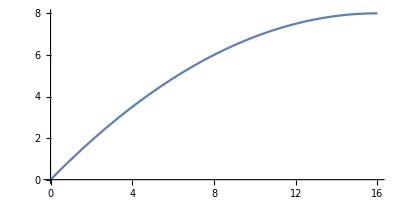

```mathematica
a1=ParametricPlot[{4t,4t-t^2/2},{t,0,4}]
```

```mathematica
g=9.85;
p1x[t_]:=16+5(t-4);
p1y[t_]:=8+3*(t-4)-1/2*g*(t-4)^2;
p2x[t_]:=16+3(t-4);
p2y[t_]:=8-3*(t-4)-1/2*g*(t-4)^2;
```

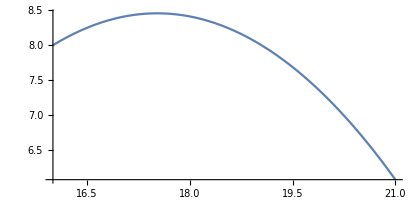

```mathematica
a2=ParametricPlot[{p1x[t],p1y[t]},{t,4,5}]
```

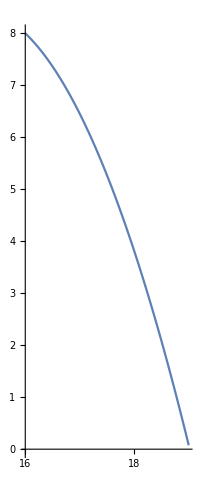

```mathematica
a3=ParametricPlot[{p2x[t],p2y[t]},{t,4,5}]
```

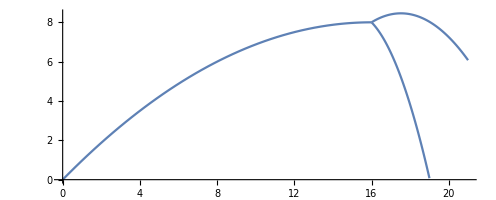

```mathematica
Show[a1,a2,a3,PlotRange->All]
```